```mathematica
f[x_] := 1 - E^-x
```

```mathematica
f''=D[f[x], {x, 2}]
```

-ⅇ^-x

```mathematica
a := 0;
b := 4;
R = -(b-a)^3/(12*n^2)
```

-4/4107

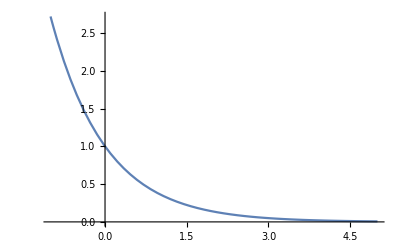

```mathematica
Plot[E^-x,{x, -1, 5}]
```

```mathematica
func[eps_] := Sqrt[16/(3*eps)]
```

```mathematica
n = Ceiling[func[10^-3]]
```

74

```mathematica
sum :=0
```

```mathematica
For[i=1, i≤n,i++,
sum += f[(i-1)/n] + f[i/n]]
result = (b-a)/(2n)sum//N
```

54.4447

1.47148

```mathematica
Integrate[f[x], {x, 0, 4}]//N
```

3.01832